```mathematica
NdS = (Gamma[d/2-del]Gamma[del])/(4 Pi Pi^(d/2));
calK = (Gamma[del/2]^2 Gamma[(d-del)/2]^2)/(Gamma[del-d/2]Gamma[d/2-del])Gamma[delPhi-del/2]^2 Gamma[delPhi - (d-del)/2]^2;
Kdel =(Pi^(d/2)Gamma[del-d/2])/Gamma[d-del] Gamma[(d-del)/2]^2/Gamma[del/2]^2;
```

```mathematica
A[nu_]:=(-nu)/(2 Pi I)(NdS/.del->delPhi)^2/Gamma[delPhi]^4 Gamma[I nu]Gamma[-I nu] Sin[Pi/2(2 delPhi-d/2+ I nu)]^2(calK /.{del->(d/2-I nu)})(Kdel/.{del->(d/2-I nu)});
```

```mathematica
A[nu]
```

(ⅈ nu π^(-3-d/2) Gamma[d/2-delPhi]^2 Gamma[delPhi+1/2 (-d/2-ⅈ nu)]^2 Gamma[delPhi+1/2 (-d/2+ⅈ nu)]^2 Gamma[1/2 (d/2+ⅈ nu)]^4 Gamma[-ⅈ nu] Sin[1/2 (-d/2+2 delPhi+ⅈ nu) π]^2)/(32 Gamma[delPhi]^2 Gamma[d/2+ⅈ nu])

```mathematica
nuNN[n_]:= - I (2 delPhi + 2n-d/2)
nuPP[n_]:= - I (2(d-delPhi)+ 2n-d/2)
nuNP[n_]:= - I (d + 2 n -d/2);
```

```mathematica
a[delta1_,delta2_,n_]:=Pochhammer[d/2,n]Pochhammer[-d+n+delta1+delta2+1,n]Pochhammer[2n+delta1+delta2,1-d/2]/(2 n! Pi^(d/2) Pochhammer[n+delta1,1-d/2]Pochhammer[n+delta2,1-d/2]Pochhammer[-d/2+n+delta1+delta2,n]);
```

```mathematica
resBAdS[delta1_,delta2_,n_]:=-1/2 a[delta1, delta2,n]/(I delta1 +I delta2-I d/2+ 2 I n);
```

```mathematica
resBdS[k_,n_]:=I/(4 Pi^2) (-I(delPhi-d/2))^2(Gamma[delPhi-d/2]Gamma[d/2-delPhi])^2 Which[k==-2, (1-Exp[I Pi (4 delPhi-d)])/Exp[-Pi nuNN[n]] resBAdS[delPhi,delPhi,n],k==2,(1-Exp[I Pi (4(d-delPhi))-d])/Exp[-Pi nuPP[n]] resBAdS[d-delPhi,d-delPhi,n] ,k==0, (-2(1-Exp[I Pi (d)]))/Exp[-Pi nuNP[n]] resBAdS[delPhi,d-delPhi,n]];
```

```mathematica
BNNminusOne[n_]:= resBdS[-2,n];
BPPminusOne[n_]:= resBdS[+2,n];
BNPminusOne[n_]:= resBdS[0,n];
```

```mathematica
ANNminusTwo[n_]:= ((-1)^n/(n!))^2(1/(-I/2))^2((A[nu]/Gamma[delPhi+1/2 (-d/2-I nu)]^2)/.{nu->nuNN[n]});
APPzero[n_]:=A[nu]/.{nu->nuPP[n]};
ANPzero[n_]:=A[nu]/.{nu->nuNP[n]};
```

```mathematica
shiftNuNN[n_]:=BNNminusOne[n]/(2(nuNN[n]^2-nuSig^2));
shiftNuPP[n_]:=BPPminusOne[n]/(2(nuPP[n]^2-nuSig^2));
shiftNuNP[n_]:=BNPminusOne[n]/(2(nuNP[n]^2-nuSig^2));
```

```mathematica
OPENN[n_]:= - I (2 ANNminusTwo[n])/BNNminusOne[n];
OPEPP[n_]:= - I g^4(2 APPzero[n])/BPPminusOne[n] shiftNuPP[n]^2;
OPENP[n_]:= - I g^4(2 ANPzero[n])/BNPminusOne[n] shiftNuNP[n]^2;
```

```mathematica
rules = {d->3, nuSig->1,delPhi ->1.11,g->1}
```

{d→3,nuSig→1,delPhi→1.11,g→1}

```mathematica
Re[(shiftNuNN[n]/.rules)/.n->20]
```

-6.63715×10^-21

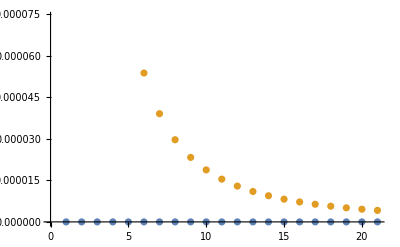

```mathematica
ListPlot[{Table[Re[shiftNuNP[n]/.rules],{n,0,20}],Table[Im[shiftNuNP[n]/.rules],{n,0,20}]}]
```

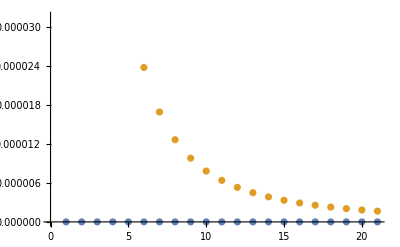

```mathematica
ListPlot[{Table[Re[shiftNuNN[n]/.rules],{n,0,20}],Table[Im[shiftNuNN[n]/.rules],{n,0,20}]}]
```

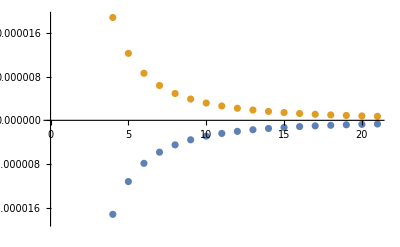

```mathematica
ListPlot[{Table[Re[shiftNuPP[n]/.rules],{n,0,20}],Table[Im[shiftNuPP[n]/.rules],{n,0,20}]}]
```

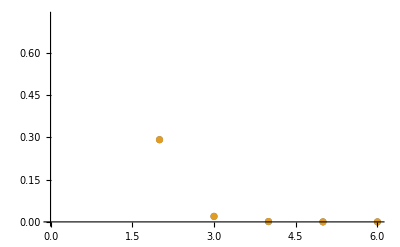

```mathematica
ListPlot[{Table[Re[OPENN[n]/.rules],{n,0,5}],Table[Re[OPENN[n]/.rules],{n,0,5}]}]
```